# Figure 2

Data are imported from julia code https://github.com/djuliannader/RabiModel

```mathematica
DatNegR50={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,1*10^(-6)},{0.95,9.6*10^(-5)},{1,0.0028721938315612316},{1.025,0.012356555259824376},{1.05,0.045046985365931436},{1.1,0.2733874102764575},{1.15,0.4362242778645884},{1.175,0.4460885111407016},{1.2,0.44040837488184037},{1.25,0.41433117514498274},{1.3,0.38455247706474105},{1.35,0.35639368013159256},{1.4,0.33087341966824346},{1.45,0.30794844862649895},{1.5,0.28734309709107686},{1.55,0.2687654993931692},{1.6,0.25195532747756655},{1.65,0.23669221450165723},{1.7,0.22278777508091752},{1.75,0.21007710233871846},{1.8,0.19843810833889042},{1.85,0.1869269263497304},{1.9,0.17789491169926075},{1.95,0.16879059428329657},{2,0.1603653371543292}};
DatPurR50={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.994775725143428},{0.7,0.9936006656401877},{0.75,0.9921537418880904},{0.8,0.9903210142961318},{0.85,0.9879003610322292},{0.9,0.9844922503337201},{0.95,0.9791771590785479},{1,0.9693224813794615},{1.025,0.9603014280895678},{1.05,0.9450674965437998},{1.1,0.8785402990262056},{1.15,0.8026871790347999},{1.2,0.7514555074649951},{1.25,0.7121302675708026},{1.3,0.6805020299580149},{1.35,0.6546746928544679},{1.4,0.6333677520262117},{1.45,0.6156417139444618},{1.5,0.600786672980406},{1.55,0.5882553764843841},{1.6,0.5776228874870241},{1.65,0.5685489740866942},{1.7,0.5607683254538206},{1.75,0.5540913609047422},{1.8,0.5482842532028399},{1.85,0.547209527765898},{1.9,0.538855080298695},{1.95,0.5350590376220995},{2,0.5316210729540178}};
DatCocR50={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2814970798851983/(3*0.6541765798996451^2)},{0.7,1.4397927565972026/(3*0.693764110355717^2)},{0.75,1.6567702540922875/(3*0.744828134343037^2)},{0.8,1.9683184699322553/(3*0.8129808049796601^2)},{0.85,2.445693875973183/(3*0.9084715246222741^2)},{0.9,3.2496856720845577/(3*1.0522287176106724^2)},{0.95,4.8151561325445025/(3*1.2942812620568696^2)},{1,8.676709177081129/(3*1.7849882071835745^2)},{1.025,13.191130472442584/(3*2.2674391149095015^2)},{1.05,22.631175113336358/(3*3.1320410019378047^2)},{1.1,86.54058048100657/(3*7.410067949519209^2)},{1.15,220.15169859326082/(3*13.300979254959833^2)},{1.2,383.911126000021/(3*18.228560986896323^2)},{1.25,582.5198428458652/(3*22.858291957216757^2)},{1.3,818.4428985824297/(3*27.38980353593512^2)},{1.35,1092.5948047408485/(3*31.877910055932638^2)},{1.4,1406.17855195663/(3*36.35409907025217^2)},{1.45,1760.7759077694393/(3*40.84098049841334^2)},{1.5,2158.2884623808554/(3*45.35588629225168^2)},{1.55,2600.874994032024/(3*49.912668152907095^2)},{1.6,3090.9451497954847/(3*54.522313513662965^2)},{1.65,3631.0354456672376/(3*59.19451141631789^2)},{1.7,4223.937966769323/(3*63.936610365068354^2)},{1.75,4964.608564499193/(3*69.40134670548123^2)},{1.8,5580.401624562337/(3*73.65252497015442^2)},{1.85,6452.280035530374/(3*78.98110097928066^2)},{1.9,7184.645185183218/(3*83.71637627393808^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
QFIPR50={{0,0},{0.05,0.0607},{0.1,0.2232},{0.2,0.6753},{0.3,1.0813},{0.4,1.3709},{0.5,1.5682},{0.6,1.7084},{0.7,1.8207},{0.8,1.9336},{0.9,2.0938},{1,2.4263},{1.05,2.6753},{1.1,2.3784},{1.2,1.4489},{1.3,1.2612},{1.4,1.1728},{1.5,1.1219},{1.6,1.0897},{1.7,1.0680},{1.8,1.0528},{1.9,1.0417},{2,1.0335}};
```

```mathematica
(*R=20*)
DatNegR100={{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,0},{0.3,0},{0.35,0},{0.4,0},{0.45,0},{0.5,0},{0.55,0},{0.6,0},{0.65,0},{0.7,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,1.9*10^(-5)},{1,0.00352991345976994},{1.05,0.16994734619626084},{1.1,0.4951335362409819},{1.15,0.48681954343363354},{1.2,0.4489441006974306},{1.25,0.4129849354026838},{1.3,0.38113406266114835},{1.35,0.35263284981942244},{1.4,0.32781379856719917},{1.45,0.3053228932107588},{1.5,0.2850804145723995},{1.55,0.26656609689781363},{1.6,0.2480970185098632},{1.65,0.23207183786995234},{1.7,0.21943236369303798},{1.75,0.2062951673978768},{1.8,0.19439519895389978},{1.85,0.1848269263497304},{1.9,0.17489491169926075},{1.95,0.16579059428329657},{2,0.1573653371543292}};
DatPurR100={{0,1},{0.05,0.9999759424382747},{0.1,0.9999034272558528},{0.15,0.9997814087135403},{0.2,0.9996080810591991},{0.25,0.999380776762398},{0.3,0.9990958075749397},{0.35,0.9987482279968808},{0.4,0.9983314878694249},{0.45,0.9978369196052229},{0.5,0.9972529689231903},{0.55,0.996564011762457},{0.6,0.9957484746508471},{0.65,0.9973066540442344},{0.7,0.9966892351069913},{0.75,0.9959203275443427},{0.8,0.994929528425102},{0.85,0.9935838821475481},{0.9,0.9915929054630556},{0.95,0.9881584656123885},{1,0.9800014736625274},{1.05,0.9422486519919183},{1.1,0.8534305724116021},{1.15,0.7929395472335256},{1.2,0.7459947586410312},{1.25,0.7083292087394012},{1.3,0.6777046890874503},{1.35,0.6531401020454791},{1.4,0.6317294496184234},{1.45,0.6143600006589414},{1.5,0.5997605091943176},{1.55,0.5874304268025001},{1.6,0.577092213637232},{1.65,0.5686073417671864},{1.7,0.560341997120267},{1.75,0.5536829994795877},{1.8,0.5489418218215516},{1.85,0.542209527765898},{1.9,0.54125080298695},{1.95,0.5380590376220995},{2,0.5346210729540178}};
DatCocR100={{0,0.7499999999999998/(3*(0.4999999999999999)^2)},{0.05,0.75187881532106897/(3*0.5006258878683949^2)},{0.1,0.7575702173461962/(3*0.5025171970312261^2)},{0.15,0.7672430711295672/(3*0.5057156865326069^2)},{0.2,0.7811926858842599/(3*0.5102937934627627^2)},{0.25,0.7998636425150817/(3*0.5163592513308773^2)},{0.3,0.8238862783538767/(3*0.5240623516549455^2)},{0.35,0.8541326243608005/(3*0.5336068437488745^2)},{0.4,0.8918015616587754/(3*0.5452661080007922^2)},{0.45,0.9385498275352047/(3*0.5594073064848732^2)},{0.5,0.996697933655965/(3*0.5765280821003401^2)},{0.55,1.0695636551744288/(3*0.5973137902315173^2)},{0.6,1.1620228587208135/(3*0.6227297910696789^2)},{0.65,1.2897951423752605/(3*0.6560073228471611^2)},{0.7,1.4544590459480515/(3*0.6968235578962798^2)},{0.75,1.6836813271448288/(3*0.75007923875338142^2)},{0.8,2.0206940023598152/(3*0.8224051511486021^2)},{0.85,2.55740536150216/(3*0.9266463261648592^2)},{0.9,3.525566992470624/(3*1.0916614134753067^2)},{0.95,5.6906269950153945/(3*1.3993451712746323^2)},{1,13.149613280222528/(3*2.200849479331304^2)},{1.05,76.11128708315083/(3*6.394523910429349^2)},{1.1,390.0769077073444/(3*17.966874862222323^2)},{1.15,852.8672071651666/(3*27.693354115657673^2)},{1.2,1466.9163467609335/(3*36.92582976004173^2)},{1.25,2231.5123618419316/(3*45.950576451022016^2)},{1.3,3146.6383171813072/(3*54.865904633018566^2)},{1.35,4227.904091396019/(3*63.62949984598251^2)},{1.4,5440.850736127636/(3*72.60824279137748^2)},{1.45,6830.976849051901/(3*81.51846803422251^2)},{1.5,8392.187334312364/(3*90.50009146062803^2)},{1.55,10133.776381520353/(3*99.57312033367347^2)},{1.6,12072.610749048303/(3*108.72358375505594^2)},{1.65,14234.255045193175/(3*117.91081940669147^2)},{1.7,16539.84077248809/(3*127.52955362315876^2)},{1.75,19101.82242230926/(3*137.1565727904349^2)},{1.8,21900.511801225963/(3*146.94181131934096^2)},{1.85,24945.598183670496/(3*156.90110285095153^2)},{1.9,28242.45205759002/(3*167.02182540075322^2)},{1.95,8089.722951897358/(3*88.8786945024876^2)},{2.0,9063.371818421145/(3*94.15939241686685^2)}};
QFIPR100={{0,0},{0.1,0.4015},{0.2,1.0099},{0.3,1.4045},{0.4,1.6287},{0.5,1.7629},{0.6,1.8543},{0.7,1.9327},{0.8,2.0284},{0.9,2.2087},{1,2.7856},{1.05,3.1546},{1.1,1.9333},{1.2,1.4149},{1.3,1.2503},{1.4,1.1676},{1.5,1.1190},{1.6,1.0880},{1.7,1.0625}};;
```

```mathematica
DatImpR50=Table[{DatPurR50[[i,1]],1-DatPurR50[[i,2]]},{i,1,Length[DatPurR50]}];
DatImpR100=Table[{DatPurR100[[i,1]],1-DatPurR100[[i,2]]},{i,1,Length[DatPurR100]}];
```

#### (a)

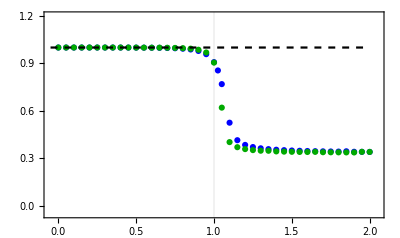

```mathematica
figtr=Show[ListPlot[{DatCocR50,DatCocR100},Joined->False,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,1.2}},(*PlotLegends->{"λ=0","λ=1/10^-5","λ=1/10"},*)PlotStyle->{{Blue,Thickness[0.0075]},{Darker[Green],Thickness[0.003]},{Red,Thickness[0.0065]}},LabelStyle->{Black,15},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[1.0,{x,-0.05,2},PlotStyle->{Dashed,Black}],AspectRatio->{0.05}]
```

#### (b)

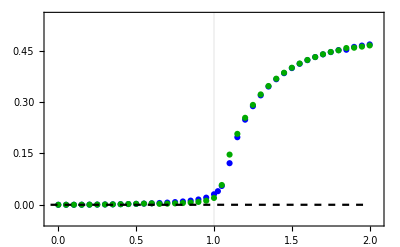

```mathematica
figimp=Show[ListPlot[{DatImpR50,DatImpR100},Joined->False,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,0.55}},PlotStyle->{{Blue,Thickness[0.0075]},{Darker[Green],Thickness[0.003]},{Red,Thickness[0.0065]}},LabelStyle->{Black,13},GridLines->{{1},{}},GridLinesStyle->{Red,{}}],Plot[0.0,{x,-0.05,2},PlotStyle->{Dashed,Black}]]
```

#### (c)

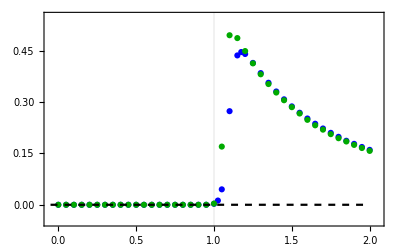

```mathematica
figneg=Show[ListPlot[{DatNegR50,DatNegR100},Joined->False,Frame->True,PlotRange->{{-0.05,2.05},{-0.05,0.55}},PlotStyle->{{Blue,Thickness[0.0075]},{Darker[Green],Thickness[0.003]},{Red,Thickness[0.0065]}},LabelStyle->{Black,13},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[0.0,{x,-0.05,2},PlotStyle->{Dashed,Black}]]
```

#### (d)

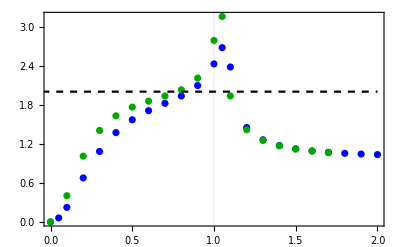

```mathematica
figQFI=Show[ListPlot[{QFIPR50,QFIPR100},Joined->False,Frame->True,PlotRange->All,PlotStyle->{{Blue,Thickness[0.0075]},{Darker[Green],Thickness[0.003]},{Red,Thickness[0.0065]}},LabelStyle->{Black,13},GridLines->{{1},{}},GridLinesStyle->{{Red},{}}],Plot[2.0,{x,-0.05,2},PlotStyle->{Dashed,Black}]]
```